### Times for Iteration

```mathematica
fulltimes1D=Table[Timing[hierIterate[{n}]][[1]],{n,1,17}];
fulltimes2D=Table[Timing[hierIterate[{n,n}]][[1]],{n,1,10}];
fulltimes3D=Table[Timing[hierIterate[{n,n,n}]][[1]],{n,1,7}];
```

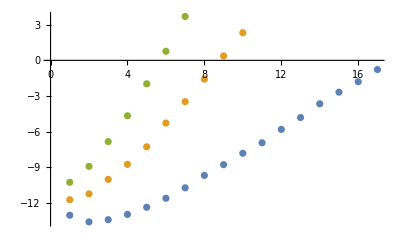

```mathematica
Show[ListPlot[{fulltimes1D,fulltimes2D,fulltimes3D}//Log2]]
```

```mathematica
(*Linear, quadratic, and cubic for the hierarchical coefficents, as desired*)
```

```mathematica
times1D=Table[Timing[sparseIterate[n,1]][[1]],{n,1,15}];
times2D=Table[Timing[sparseIterate[n,2]][[1]],{n,1,15}];
times3D=Table[Timing[sparseIterate[n,3]][[1]],{n,1,15}];
```

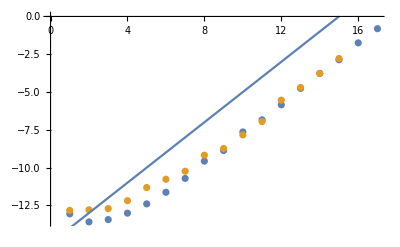

```mathematica
Show[ListPlot[{Table[Timing[hierIterate[{n}]][[1]],{n,1,17}],times1D}//Log2],Plot[x-15,{x,1,15}]]
```

```mathematica
(*Sparse and Hier times are the same at 1D, because it should be the same algorithm*)
```

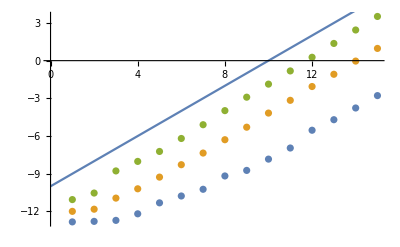

```mathematica
Show[ListPlot[{times1D,times2D,times3D}//Log2],Plot[x-10,{x,0,15}]]
```

```mathematica
(*Note how they are all linear. This is why we like Sparse grids :) *)
```

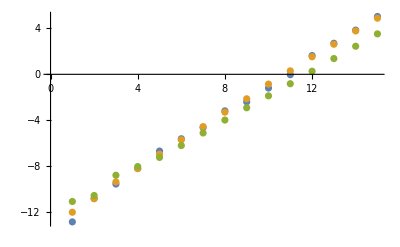

```mathematica
ListPlot[{times1D Table[n^2,{n,1,15}],times2D Table[n,{n,1,15}],times3D}//Log2]
```

```mathematica
(*The times are logarithmic factors of each other*)
```

### Times for Finding Coefficients

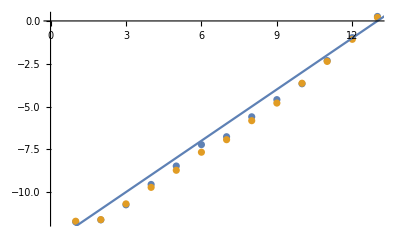

```mathematica
Show[ListPlot[{Table[Timing[fullCoefficients[Sin[Pi #[[1]]]&,{n}]][[1]],{n,1,13}],Table[Timing[sparseCoefficients[Sin[Pi #[[1]]]&,n,1]][[1]],{n,1,13}]}//Log2],Plot[x-13,{x,0,14}]]
```

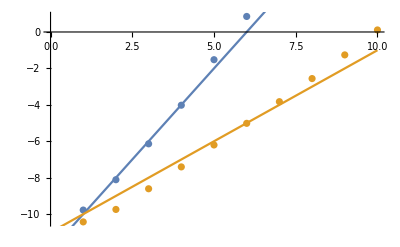

```mathematica
Show[ListPlot[{Table[Timing[fullCoefficients[Sin[Pi#[[1]]+#[[2]]]&,{n,n}]][[1]],{n,1,6}],Table[Timing[sparseCoefficients[Sin[Pi#[[1]]+#[[2]]]&,n,2]][[1]],{n,1,10}]}//Log2],Plot[{2x-12,x-11},{x,0,10}]]
```

```mathematica
(*Linear, and the slight non-linearity comes from computing derivatives*)
```